```mathematica
Clear[hbar, e0, m0, ηm];
hbar=6.58211899*10^(-16);  (* h/2π  in eV s *)
m0=9.10938215*10^(-31); 
e0=1.602176487*10^(-19);
ηm=hbar^2*e0*10^(20)/m0;  (* hbar^2/m0 in eV A^2 *)
μB=5.7883818066 * 10^(-2);    (* in meV/T *)
meVpK=8.6173325*10^(-2);   (* Kelvin into meV *)
(* **************************************** *)
```

```mathematica
Clear[ts, tsw, as, ms, Nx, Ny, Nxn, α, αw, Δ];
as=100.0; (* unit cell in A *)
ms=0.02;
ts=500*ηm/(2*as^2*ms); (* hopping in meV *)
α=200.0/as; (* Rashba coupling in meV *)
Δ=0.4; (* induced gap in meV *)
Nx=250;
NxM=40;
Nxn=0;
Ny=1;
asw=600.0/(Ny+1);
αw=α*as/asw;
tsw=4.0;
μ=0.0;
B=2Δ;

(*
(*Turns off blue and red*)
tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.0;
θ1=1.0π;
θM=0.1 π;
θ2=0.0 π;
θ3=0.5π;
*)

tϕ1=0.4ts;
tϕ2=0.4ts;
tϕ3=0.4ts;
αϕ=0.5 π;
θ1=1.0π;
θM=0.1 π;
θ2=0.5 π;
θ3=0.5π;

ϕ=0.0 π;
ϕ3=0;
```

```mathematica
ψA1L={};
ψAML={};
ψA2L={};
ψA3L={};

ψB1L={};
ψBML={};
ψB2L={};
ψB3L={};


For[θM=0,θM≤2 π,θM+=0.1,
ϵ0=2ts Cos[Pi/(Nx+1.0)];
(*First Chain*)
H1σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ1],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H1σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{Nx,Nx}];
H1σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ1],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{Nx,Nx}];

H1σ12τ12=SparseArray[{Band[{1,1}]->Δ},{Nx,Nx}];
H1σ21τ12=SparseArray[{Band[{1,1}]->-Δ},{Nx,Nx}];

H1τ11=SparseArray[ArrayFlatten[{{H1σ11τ11,H1σ12τ11},{H1σ21τ11,H1σ22τ11}}]];
H1τ22=-H1τ11;
H1τ12=SparseArray[ArrayFlatten[{{0,H1σ12τ12},{H1σ21τ12,0}}]];
H1τ21=Conjugate[Transpose[H1τ12]];

H11=SparseArray[ArrayFlatten[{{H1τ11,H1τ12},{H1τ21,H1τ22}}]];


(*Middle Chain*)
HMσ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θM],Band[{1,2}]->ts,Band[{2,1}]->ts},{NxM,NxM}];
HMσ12τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->α/2,Band[{2,1}]->-α/2},{NxM,NxM}];
HMσ21τ11=SparseArray[{Band[{1,1}]->B Cos[θM],Band[{1,2}]->-α/2,Band[{2,1}]->α/2},{NxM,NxM}];

HMσ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];
HMσ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{NxM,NxM}];

HMτ11=SparseArray[ArrayFlatten[{{HMσ11τ11,HMσ12τ11},{HMσ21τ11,HMσ22τ11}}]];
HMτ22=-HMτ11;
HMτ12=SparseArray[ArrayFlatten[{{0,HMσ12τ12},{HMσ21τ12,0}}]];
HMτ21=Conjugate[Transpose[HMτ12]];

HMM=SparseArray[ArrayFlatten[{{HMτ11,HMτ12},{HMτ21,HMτ22}}]];


(*Second Chain*)
H2σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ2],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H2σ12τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2(Cos[αϕ]+ⅈ Sin[αϕ]),Band[{2,1}]->α/2(-Cos[αϕ]+ⅈ Sin[αϕ])},{Nx,Nx}];
H2σ21τ11=SparseArray[{Band[{1,1}]->B Cos[θ2],Band[{1,2}]->α/2(-Cos[αϕ]-ⅈ Sin[αϕ]),Band[{2,1}]->α/2(Cos[αϕ]-ⅈ Sin[αϕ])},{Nx,Nx}];

H2σ12τ12=SparseArray[{Band[{1,1}]->Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];
H2σ21τ12=SparseArray[{Band[{1,1}]->-Δ ⅇ^(ⅈ ϕ)},{Nx,Nx}];

H2τ11=SparseArray[ArrayFlatten[{{H2σ11τ11,H2σ12τ11},{H2σ21τ11,H2σ22τ11}}]];
H2τ22=-H2τ11;
H2τ12=SparseArray[ArrayFlatten[{{0,H2σ12τ12},{H2σ21τ12,0}}]];
H2τ21=Conjugate[Transpose[H2τ12]];

H22=SparseArray[ArrayFlatten[{{H2τ11,H2τ12},{H2τ21,H2τ22}}]];

(*Third Chain*)
H3σ11τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0+B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ22τ11=SparseArray[{Band[{1,1}]->-μ+ϵ0-B Sin[θ3],Band[{1,2}]->ts,Band[{2,1}]->ts},{Nx,Nx}];
H3σ12τ11=SparseArray[{Band[{1,1}]->ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];
H3σ21τ11=SparseArray[{Band[{1,1}]->-ⅈ B Cos[θ3],Band[{1,2}]->-ⅈ α/2,Band[{2,1}]->ⅈ α/2},{Nx,Nx}];

H3σ12τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];
H3σ21τ12=SparseArray[{Band[{1,1}]->ⅈ Δ ⅇ^(ⅈ ϕ3)},{Nx,Nx}];

H3τ11=SparseArray[ArrayFlatten[{{H3σ11τ11,H3σ12τ11},{H3σ21τ11,H3σ22τ11}}]];
H3τ22=-H3τ11;
H3τ12=SparseArray[ArrayFlatten[{{0,H3σ12τ12},{H3σ21τ12,0}}]];
H3τ21=Conjugate[Transpose[H3τ12]];

H33=SparseArray[ArrayFlatten[{{H3τ11,H3τ12},{H3τ21,H3τ22}}]];

(*Tunnel Junction*)
H1M=SparseArray[{{Nx,1}->tϕ1,{2Nx,NxM+1}->tϕ1,{3Nx,2NxM+1}->-tϕ1,{4Nx,3NxM+1}->-tϕ1},{4Nx,4NxM}];
HM1=Conjugate[Transpose[H1M]];

HM2=SparseArray[{{NxM,1}->tϕ2,{2NxM,Nx+1}->tϕ2,{3NxM,2Nx+1}->-tϕ2,{4NxM,3Nx+1}->-tϕ2},{4NxM,4Nx}];
H2M=Conjugate[Transpose[HM2]];

HM3=SparseArray[{{NxM/2,1}->tϕ3,{NxM+NxM/2,Nx+1}->tϕ3,{2NxM+NxM/2,2Nx+1}->-tϕ3,{3NxM+NxM/2,3Nx+1}->-tϕ3},{4NxM,4Nx}];
H3M=Conjugate[Transpose[HM3]];

(*Full Wire*)
Hsp=SparseArray[ArrayFlatten[{{H11,H1M,0,0},{HM1,HMM,HM2,HM3},{0,H2M,H22,0},{0,H3M,0,H33}}]];

{e,ψ}=Transpose[Sort[Transpose[Eigensystem[Hsp,-10]]]];



n=5;
Print[{θM,e[[n]],e[[n-1]]}];
ψA1ue=Table[{i-1,Abs[ψ[[n,i]]]},{i,1,Nx}];
ψAMue=Table[{i-1-3Nx,Abs[ψ[[n,i]]]},{i,4Nx,4Nx+NxM}];
ψA2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψA3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];




e[[n-1]];
ψB1ue=Table[{i-1,Abs[ψ[[n-1,i]]]},{i,1,Nx}];
ψBMue=Table[{i-1-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx,4Nx+NxM}];
ψB2ue=Table[{i-1-3Nx-3NxM,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM,4Nx+4NxM+Nx}];
ψB3ue=Table[{i-1-3Nx-3NxM-3Nx,Abs[ψ[[n-1,i]]]},{i,4Nx+4NxM+4Nx,4Nx+4NxM+4Nx+Nx}];

ψA1L=Join[ψA1L,{ψA1ue}];
ψAML=Join[ψAML,{ψAMue}];
ψA2L=Join[ψA2L,{ψA2ue}];
ψA3L=Join[ψA3L,{ψA3ue}];

ψB1L=Join[ψB1L,{ψB1ue}];
ψBML=Join[ψBML,{ψBMue}];
ψB2L=Join[ψB2L,{ψB2ue}];
ψB3L=Join[ψB3L,{ψB3ue}];

];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{0,-2.29364×10^-7,-2.97582×10^-7}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

{0.1,-2.35571×10^-7,-2.97368×10^-7}

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

General::stop: Further output of Eigensystem::maxit2 will be suppressed during this calculation.

{0.2,-2.38855×10^-7,-2.96857×10^-7}

{0.3,-2.38795×10^-7,-2.95932×10^-7}

{0.4,-2.35347×10^-7,-2.94733×10^-7}

{0.5,-2.28926×10^-7,-2.93536×10^-7}

{0.6,-2.2033×10^-7,-2.92502×10^-7}

{0.7,-2.10484×10^-7,-2.91646×10^-7}

{0.8,-2.00196×10^-7,-2.9092×10^-7}

{0.9,-1.90054×10^-7,-2.90272×10^-7}

{1.,-1.80421×10^-7,-2.89662×10^-7}

{1.1,-1.71491×10^-7,-2.89065×10^-7}

{1.2,-1.63343×10^-7,-2.88464×10^-7}

{1.3,-1.55985×10^-7,-2.87852×10^-7}

{1.4,-1.49381×10^-7,-2.87224×10^-7}

{1.5,-1.43479×10^-7,-2.86578×10^-7}

{1.6,-1.38217×10^-7,-2.85916×10^-7}

{1.7,-1.33533×10^-7,-2.85238×10^-7}

{1.8,-1.29368×10^-7,-2.84548×10^-7}

{1.9,-1.25666×10^-7,-2.83848×10^-7}

{2.,-1.2238×10^-7,-2.83145×10^-7}

{2.1,-1.19465×10^-7,-2.82441×10^-7}

{2.2,-1.16884×10^-7,-2.81744×10^-7}

{2.3,-1.14604×10^-7,-2.81059×10^-7}

{2.4,-1.12595×10^-7,-2.80391×10^-7}

{2.5,-1.10833×10^-7,-2.79749×10^-7}

{2.6,-1.09298×10^-7,-2.79139×10^-7}

{2.7,-1.0797×10^-7,-2.78568×10^-7}

{2.8,-1.06835×10^-7,-2.78043×10^-7}

{2.9,-1.05879×10^-7,-2.77572×10^-7}

{3.,-1.05093×10^-7,-2.77161×10^-7}

{3.1,-1.04468×10^-7,-2.76818×10^-7}

{3.2,-1.03998×10^-7-1.63917×10^-15 ⅈ,-2.76548×10^-7}

{3.3,-1.03678×10^-7,-2.76357×10^-7}

{3.4,-1.03506×10^-7,-2.76251×10^-7}

{3.5,-1.03481×10^-7,-2.76234×10^-7}

{3.6,-1.03605×10^-7,-2.76309×10^-7}

{3.7,-1.0388×10^-7,-2.76479×10^-7}

{3.8,-1.04312×10^-7,-2.76745×10^-7}

{3.9,-1.04908×10^-7,-2.77108×10^-7}

{4.,-1.05677×10^-7,-2.77565×10^-7}

{4.1,-1.06634×10^-7,-2.78115×10^-7}

{4.2,-1.07791×10^-7,-2.78753×10^-7}

{4.3,-1.09168×10^-7,-2.79474×10^-7}

{4.4,-1.10787×10^-7,-2.80273×10^-7}

{4.5,-1.12673×10^-7,-2.8114×10^-7}

{4.6,-1.14856×10^-7,-2.82069×10^-7}

{4.7,-1.17371×10^-7,-2.8305×10^-7}

{4.8,-1.20257×10^-7+2.38714×10^-15 ⅈ,-2.84074×10^-7}

{4.9,-1.23561×10^-7,-2.85129×10^-7}

{5.,-1.27334×10^-7,-2.86207×10^-7}

{5.1,-1.31634×10^-7,-2.87298×10^-7}

{5.2,-1.36523×10^-7,-2.88392×10^-7}

{5.3,-1.4207×10^-7,-2.89481×10^-7}

{5.4,-1.48342×10^-7,-2.90557×10^-7}

{5.5,-1.554×10^-7,-2.91615×10^-7}

{5.6,-1.63293×10^-7,-2.9265×10^-7}

{5.7,-1.72032×10^-7,-2.93658×10^-7}

{5.8,-1.8157×10^-7,-2.94634×10^-7}

{5.9,-1.91762×10^-7,-2.9557×10^-7}

{6.,-2.0232×10^-7,-2.96443×10^-7}

{6.1,-2.12774×10^-7,-2.97185×10^-7}

{6.2,-2.22461×10^-7,-2.97579×10^-7}

```mathematica
1.2/π
```

0.381972

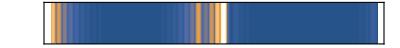

```mathematica
nt=48;
ψbar=Join[ψA1L[[nt]],ψAML[[nt]],ψA2L[[nt]]];
ψbarC=Join[Table[{i,0.0,ψbar[[i,2]]},{i,1,Length[ψbar]}],Table[{i,1.0,ψbar[[i,2]]},{i,1,Length[ψbar]}]];
bar=ListContourPlot[ψbarC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->1/10,FrameTicks->None]
```

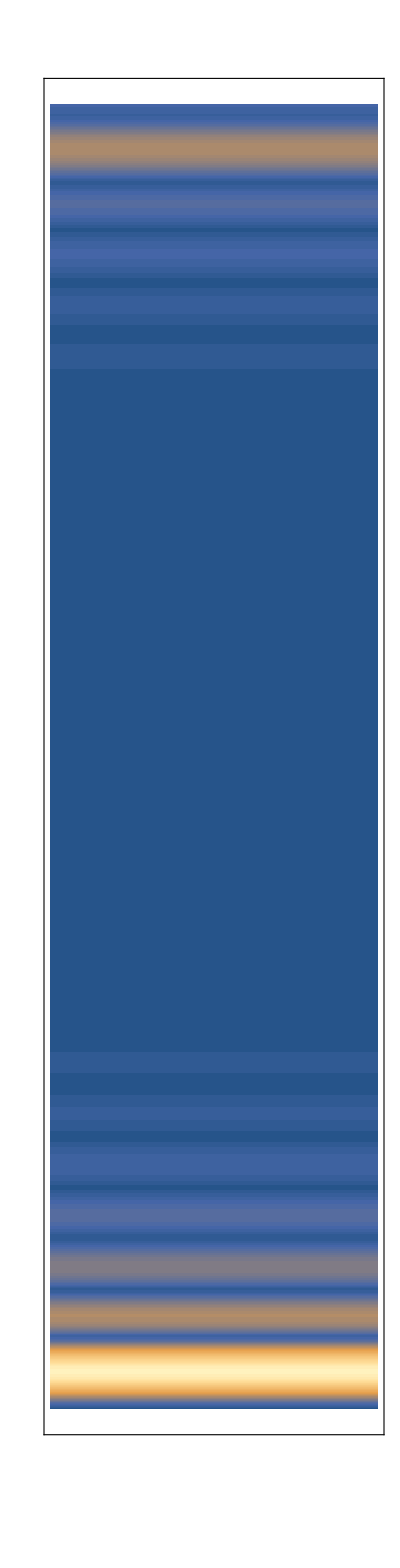

```mathematica
nt=48;
ψleg=ψA3L[[nt]];
ψlegC=Join[Table[{0.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}],Table[{1.0,Length[ψleg]-i,ψleg[[i,2]]},{i,1,Length[ψleg]}]];
leg=ListContourPlot[ψlegC,PlotRange->{0,0.1},Contours->100,ContourStyle->None,AspectRatio->10/1,FrameTicks->None]
```

```mathematica
Manipulate[ListPlot[{ψA1L[[nt]],ψAML[[nt]],ψA2L[[nt]],ψA3L[[nt]]},Joined->True,PlotRange->All],{nt,1,Length[ψA1L],1}]
```

```mathematica
Manipulate[ListPlot[{ψB1L[[nt]],ψBML[[nt]],ψB2L[[nt]],ψB3L[[nt]]},Joined->True,PlotRange->All],{nt,1,Length[ψB1L],1}]
```